```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/862nm.dat"]
```

{{1.65577,-0.216689},{1.59352,-0.231365},{1.51672,-0.202434},{1.46373,-0.210869},{1.42047,-0.18205},{1.37769,-0.224107},{1.34607,-0.183502},{1.31418,-0.198024},{1.27734,-0.19582},{1.24989,-0.212167},{1.21939,-0.174425},{1.20221,-0.225597},{1.18519,-0.417654},{1.17023,-0.617112},{1.1572,-0.766234},{1.14604,-0.911353},{1.13497,-1.13728},{1.12762,-7.06568},{1.12192,-3.45387},{1.11852,-2.53746},{1.11638,-1.9563},{1.11532,-1.67259},{1.11466,-0.711882},{1.11691,-0.452572},{1.12052,-0.274226},{1.12514,-0.199085},{1.15252,-0.17927},{1.18204,-0.210684},{1.20774,-0.12638},{1.24068,-0.132401},{1.28541,-0.137115},{1.36328,-0.142301},{1.4246,-0.131853}}

-5.06014+3.41589 x

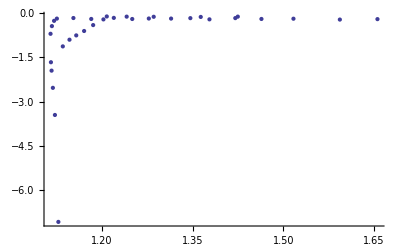

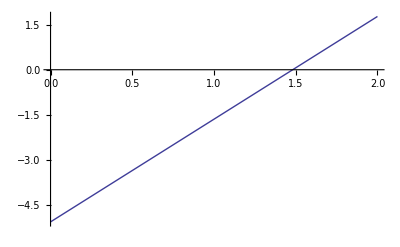

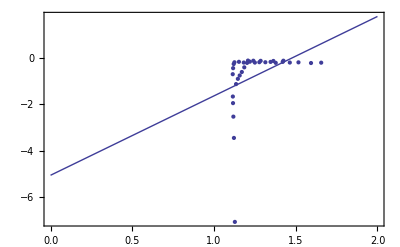

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```